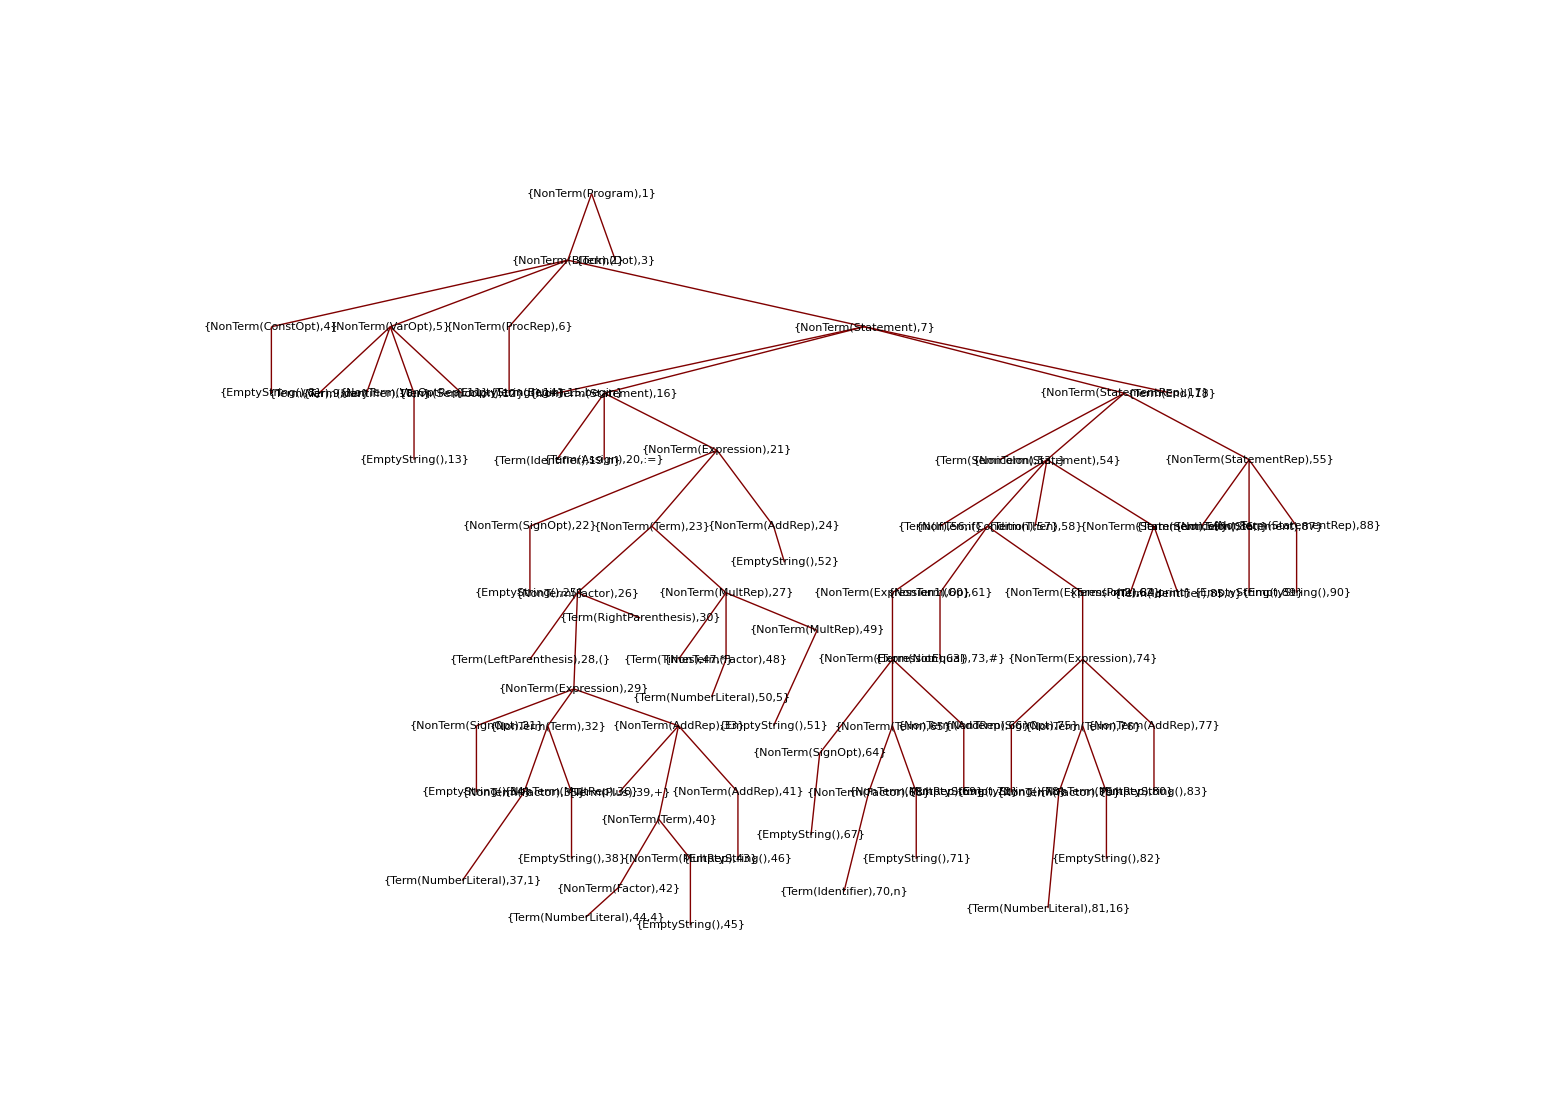

```mathematica
tinyProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
      print n;
end.";
```

```mathematica
tokens = Tokenize[tinyProgram,symbolTokens,keywordDFA];
```

```mathematica
parseTree = Parse[tokens,grammar] ;
SynthesizeTree[parseTree]
```

{{NonTerm[Program],1}[TACode]→$341 = 1+4
$342 = $341*5
n = $342
$343 = n!=16
if_false $343 goto L$344
print n
label L$344
halt,{NonTerm[Block],2}[Value]→,{NonTerm[Block],2}[TACode]→$341 = 1+4
$342 = $341*5
n = $342
$343 = n!=16
if_false $343 goto L$344
print n
label L$344,{NonTerm[Statement],7}[Value]→,{NonTerm[Statement],7}[TACode]→$341 = 1+4
$342 = $341*5
n = $342
$343 = n!=16
if_false $343 goto L$344
print n
label L$344,{NonTerm[StatementRep],17}[Value]→,{NonTerm[StatementRep],17}[TACode]→$343 = n!=16
if_false $343 goto L$344
print n
label L$344,{NonTerm[StatementRep],55}[Value]→,{NonTerm[StatementRep],55}[TACode]→,{NonTerm[StatementRep],88}[Value]→,{NonTerm[StatementRep],88}[TACode]→,{NonTerm[Statement],87}[Value]→,{NonTerm[Statement],87}[TACode]→,{Term[Semicolon],86}[Value]→;,{NonTerm[Statement],54}[Value]→$344,{NonTerm[Statement],54}[TACode]→$343 = n!=16
if_false $343 goto L$344
print n
label L$344,{NonTerm[Statement],59}[Value]→,{NonTerm[Statement],59}[TACode]→print n,{Term[Identifier],85}[Value]→n,{Term[Print],84}[Value]→print,{NonTerm[Condition],57}[Value]→$343,{NonTerm[Condition],57}[TACode]→$343 = n!=16,{NonTerm[Expression2],62}[Value]→16,{NonTerm[Expression2],62}[TACode]→,{NonTerm[Expression],74}[Value]→16,{NonTerm[Expression],74}[TACode]→,{NonTerm[AddRep],77}[Value]→,{NonTerm[AddRep],77}[TACode]→,{NonTerm[AddRep],77}[Op]→,{NonTerm[Term],76}[Value]→16,{NonTerm[Term],76}[TACode]→,{NonTerm[MultRep],80}[Value]→,{NonTerm[MultRep],80}[TACode]→,{NonTerm[MultRep],80}[Op]→,{NonTerm[Factor],79}[Value]→16,{NonTerm[Factor],79}[TACode]→,{Term[NumberLiteral],81}[Value]→16,{NonTerm[SignOpt],75}[Value]→,{NonTerm[Op],61}[Value]→!=,{Term[NotEqual],73}[Value]→#,{NonTerm[Expression1],60}[Value]→n,{NonTerm[Expression1],60}[TACode]→,{NonTerm[Expression],63}[Value]→n,{NonTerm[Expression],63}[TACode]→,{NonTerm[AddRep],66}[Value]→,{NonTerm[AddRep],66}[TACode]→,{NonTerm[AddRep],66}[Op]→,{NonTerm[Term],65}[Value]→n,{NonTerm[Term],65}[TACode]→,{NonTerm[MultRep],69}[Value]→,{NonTerm[MultRep],69}[TACode]→,{NonTerm[MultRep],69}[Op]→,{NonTerm[Factor],68}[Value]→n,{NonTerm[Factor],68}[TACode]→,{Term[Identifier],70}[Value]→n,{NonTerm[SignOpt],64}[Value]→,{Term[If],56}[Value]→if,{Term[Semicolon],53}[Value]→;,{NonTerm[Statement],16}[Value]→,{NonTerm[Statement],16}[TACode]→$341 = 1+4
$342 = $341*5
n = $342,{NonTerm[Expression],21}[Value]→$342,{NonTerm[Expression],21}[TACode]→$341 = 1+4
$342 = $341*5,{NonTerm[AddRep],24}[Value]→,{NonTerm[AddRep],24}[TACode]→,{NonTerm[AddRep],24}[Op]→,{NonTerm[Term],23}[Value]→$342,{NonTerm[Term],23}[TACode]→$341 = 1+4
$342 = $341*5,{NonTerm[MultRep],27}[Value]→5,{NonTerm[MultRep],27}[TACode]→,{NonTerm[MultRep],27}[Op]→*,{NonTerm[MultRep],49}[Value]→,{NonTerm[MultRep],49}[TACode]→,{NonTerm[MultRep],49}[Op]→,{NonTerm[Factor],48}[Value]→5,{NonTerm[Factor],48}[TACode]→,{Term[NumberLiteral],50}[Value]→5,{Term[Times],47}[Value]→*,{NonTerm[Factor],26}[Value]→$341,{NonTerm[Factor],26}[TACode]→$341 = 1+4,{NonTerm[Expression],29}[Value]→$341,{NonTerm[Expression],29}[TACode]→$341 = 1+4,{NonTerm[AddRep],33}[Value]→4,{NonTerm[AddRep],33}[TACode]→,{NonTerm[AddRep],33}[Op]→+,{NonTerm[AddRep],41}[Value]→,{NonTerm[AddRep],41}[TACode]→,{NonTerm[AddRep],41}[Op]→,{NonTerm[Term],40}[Value]→4,{NonTerm[Term],40}[TACode]→,{NonTerm[MultRep],43}[Value]→,{NonTerm[MultRep],43}[TACode]→,{NonTerm[MultRep],43}[Op]→,{NonTerm[Factor],42}[Value]→4,{NonTerm[Factor],42}[TACode]→,{Term[NumberLiteral],44}[Value]→4,{Term[Plus],39}[Value]→+,{NonTerm[Term],32}[Value]→1,{NonTerm[Term],32}[TACode]→,{NonTerm[MultRep],36}[Value]→,{NonTerm[MultRep],36}[TACode]→,{NonTerm[MultRep],36}[Op]→,{NonTerm[Factor],35}[Value]→1,{NonTerm[Factor],35}[TACode]→,{Term[NumberLiteral],37}[Value]→1,{NonTerm[SignOpt],31}[Value]→,{Term[LeftParenthesis],28}[Value]→(,{NonTerm[SignOpt],22}[Value]→,{Term[Assign],20}[Value]→:=,{Term[Identifier],19}[Value]→n,{Term[Begin],15}[Value]→begin,{Term[Identifier],10}[Value]→n,{Term[Var],9}[Value]→var}